```mathematica
Kc b + Kc (-c)(n-1)+Kc b (n-2)//Simplify
```

(b-c) Kc (-1+n)

```mathematica
XX=(1-Qout)(-c + Kc (-c) + b Kcin )+ (Qin-Qout)(b + Kc b + Kcin (-c)(n-1)+Kcin b (n-2))/.{Kc->-((1-m)^2/n+m^2/(n d-n)),Kcin->-((1-m)^2/n+m^2/(n d -n))}
```

(-c+b (-(1-m)^2/n-m^2/(-n+d n))-c (-(1-m)^2/n-m^2/(-n+d n))) (1-Qout)+(b+b (-(1-m)^2/n-m^2/(-n+d n))+b (-2+n) (-(1-m)^2/n-m^2/(-n+d n))-c (-1+n) (-(1-m)^2/n-m^2/(-n+d n))) (Qin-Qout)

```mathematica
BH=(b + Kc b + Kcin (-c)(n-1)+Kcin b (n-2))/.Kcin->Kc/.{Kc->-((1-m)^2/n+m^2/(n d-n))}//FullSimplify
CH=-(-c + Kc (-c) + b Kcin )/.Kcin->Kc/.{Kc->-((1-m)^2/n+m^2/(n d-n))}//FullSimplify
```

(c (-1+d (-1+m)^2+2 m) (-1+n)+b (-1+2 m+d (1-(-2+m) m (-1+n))-2 m n))/((-1+d) n)

c+((b-c) (-1+d (-1+m)^2+2 m))/((-1+d) n)

```mathematica
prms={b->15,c->1,d->15,n->4}
```

{b→15,c→1,d→15,n→4}

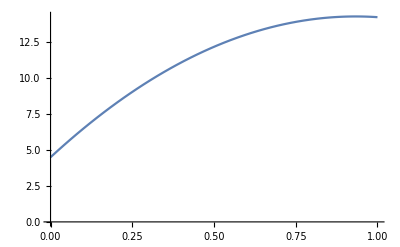

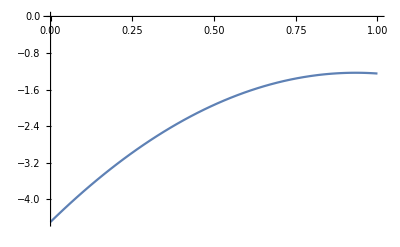

```mathematica
Plot[BH/.prms,{m,0,1},AxesOrigin->{0,0}]
Plot[-CH/.prms,{m,0,1},AxesOrigin->{0,0}]
```

```mathematica
QinM=-((-1+μ) (μ-d μ+m (-1+d μ)))/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ));
```

```mathematica
QoutM=(m (-1+μ))/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ));
QinWF=(-d+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))/(d (-1+n)+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2));
QoutWF=(-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))/(d (-1+n)+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2));
```

```mathematica
R2M=(Qin-Qout)/(1-Qout)/.{Qin->QinM,Qout->QoutM};
R2WF=(Qin-Qout)/(1-Qout)/.{Qin->QinWF,Qout->QoutWF};
```

```mathematica
R2M//FullSimplify
rrr=Limit[R2M,d->∞]//FullSimplify
Factor[Numerator[rrr]]
FullSimplify[Denominator[rrr]]
```

-((1+d (-1+m)) (-1+μ))/(1+(-1+n) μ+d (-1+m (-1+n) (-1+μ)+μ-n μ))

(-1+m+μ-m μ)/(-1+m (-1+n) (-1+μ)+μ-n μ)

-(-1+m) (-1+μ)

-1+m (-1+n) (-1+μ)+μ-n μ

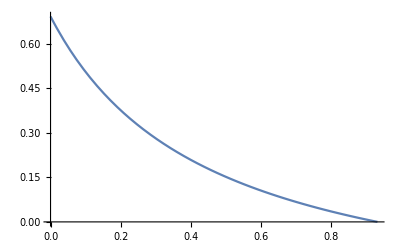

```mathematica
Plot[R2M/.prms/.μ->0.1,{m,0,(d-1)/d/.prms},AxesOrigin->{0,0}]
```

```mathematica
D[R2M,m]//FullSimplify
D[R2WF,m]//FullSimplify
Solve[%==0,m]
```

((-1+d) d n (-1+μ))/(1+(-1+n) μ+d (-1+m (-1+n) (-1+μ)+μ-n μ))^2

(2 (-1+d)^2 d (1+d (-1+m)) n (-1+μ)^2)/(-1+d (2 (1+m (-1+n))+d (-1+(-2+m) m (-1+n)))+2 μ-2 (d (2+d (-1+m)) (-1+m) (-1+n)+n) μ+(1+d (-1+m))^2 (-1+n) μ^2)^2

{{m→(-1+d)/d}}

```mathematica
Collect[XX,{b,c},FullSimplify]
```

1/((-1+d) n)c (-1+n+Qin-n Qin+2 m (1+(-1+n) Qin-n Qout)+d ((-1+n) (-1+Qin)+m^2 (1+(-1+n) Qin-n Qout)+2 m (-1+Qin-n Qin+n Qout)))+(b (1-Qin+2 m (-1+Qin-n Qin+n Qout)+d (-1+Qin+(-2+m) m (-1+Qin-n Qin+n Qout))))/((-1+d) n)

```mathematica
Assuming[c>0,FullSimplify[(XX/.b->0)/-c/.Qout->0]]
```

-(-1+d+2 m-2 d m+d m^2+n-d n+(-1+d (-1+m)^2+2 m) (-1+n) Qin)/((-1+d) n)

```mathematica
β=Qin-(1/n+((n-1)Qin)/n)((1-m)^2+m^2/(d -1))-Qout (2m(1-m)+(d-2)m^2/(d-1))
```

Qin-((1-m)^2+m^2/(-1+d)) (1/n+((-1+n) Qin)/n)-(2 (1-m) m+((-2+d) m^2)/(-1+d)) Qout

```mathematica
bb=Assuming[c>0,FullSimplify[(XX/.c->0)/b]]//FullSimplify
```

(1-Qin+2 m (-1+Qin-n Qin+n Qout)+d (-1+Qin+(-2+m) m (-1+Qin-n Qin+n Qout)))/((-1+d) n)

```mathematica
bb-β//FullSimplify
```

0

```mathematica
γ=1+-(1/n+((n-1)Qin)/n)((1-m)^2+m^2/(d -1))-Qout (2m(1-m)+(d-2)m^2/(d-1))
```

1+((1-m)^2+m^2/(-1+d)) (-1/n-((-1+n) Qin)/n)-(2 (1-m) m+((-2+d) m^2)/(-1+d)) Qout

```mathematica
cc=Assuming[c>0,FullSimplify[(XX/.b->0)/-c]]
```

1/((-1+d) n)((-1+n) (-1+Qin)+2 m (-1+Qin-n Qin+n Qout)+d (-1+n+Qin-n Qin+2 m (1+(-1+n) Qin-n Qout)+m^2 (-1+Qin-n Qin+n Qout)))

```mathematica
cc-γ//FullSimplify
```

0

```mathematica
D[BH,m]//FullSimplify
Solve[%==0]

D[CH,m]//FullSimplify
Solve[%==0]
```

-(2 (b-c) (1+d (-1+m)) (-1+n))/((-1+d) n)

{{c→b},{m→(-1+d)/d},{n→1}}

((b-c) (2+2 d (-1+m)))/((-1+d) n)

{{c→b},{m→(-1+d)/d}}